## Introduction

Making pics for paper here

## Fixed points

### Equations

#### Defintions

```mathematica
Clear[b,j,k,e,xp,xm,θp,θm];
es={
e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->k/.b->1;
TableForm[es]
```

e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

#### Prepare

```mathematica
tempSub=Solve[es[[{1,3}]]=={0,0},{xm,θm}]/.C[1]->0/.C[2]->0;
TableForm[tempSub]
```

xm→π-ArcSin[e Sec[xp]] | θm→π-ArcSin[e Sec[θp]]
xm→π-ArcSin[e Sec[xp]] | θm→ArcSin[e Sec[θp]]
xm→ArcSin[e Sec[xp]] | θm→π-ArcSin[e Sec[θp]]
xm→ArcSin[e Sec[xp]] | θm→ArcSin[e Sec[θp]]

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
TableForm[etemp]
```

√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

There are 4 batches

1. √(1-e^2 Sec[xp]^2) = 0 & √(1-e^2 Sec[θp]^2)= 0. 
2. (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp]) = 0 & (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])= 0.
3. √(1-e^2 Sec[xp]^2) = 0 &(e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp]) = 0.
4. (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp]) = 0 & √(1-e^2 Sec[θp]^2) = 0.

#### Order parameter definition

```mathematica
e3={xp==1/2(x1+x2),xm==1/2(x1-x2),θp==1/2(θ1+θ2),θm==1/2(θ1-θ2)};
sub3=Solve[e3,{x1,x2,θ1,θ2}];
Wp=1/2(Exp[ⅈ(x1+θ1)]+Exp[ⅈ(x2+θ2)]);
Wm=1/2(Exp[ⅈ(x1-θ1)]+Exp[ⅈ(x2-θ2)]);
{Wp,Wm}=({Wp,Wm}/.sub3[[1]])//ExpToTrig//FullSimplify;
Wm=ExpToTrig[Wm]//Simplify;
TableForm[{Wp,Wm}]
```

Cos[xm+θm] (Cos[xp+θp]+ⅈ Sin[xp+θp])
Cos[xm-θm] (Cos[xp-θp]+ⅈ Sin[xp-θp])

### Fixed point 1

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e11={etemp[[1,1]],etemp[[2,1]]}//FullSimplify;
TableForm[e11]
fp1=Solve[e11==0,{xp,θp}]//FullSimplify
Length[fp3]
```

√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

√(1-e^2 Sec[xp]^2)
√(1-e^2 Sec[θp]^2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp→-ArcCos[-e],θp→-ArcCos[-e]},{xp→-ArcCos[-e],θp→ArcCos[-e]},{xp→-ArcCos[-e],θp→-ArcCos[e]},{xp→-ArcCos[-e],θp→ArcCos[e]},{xp→ArcCos[-e],θp→-ArcCos[-e]},{xp→ArcCos[-e],θp→ArcCos[-e]},{xp→ArcCos[-e],θp→-ArcCos[e]},{xp→ArcCos[-e],θp→ArcCos[e]},{xp→-ArcCos[e],θp→-ArcCos[-e]},{xp→-ArcCos[e],θp→ArcCos[-e]},{xp→-ArcCos[e],θp→-ArcCos[e]},{xp→-ArcCos[e],θp→ArcCos[e]},{xp→ArcCos[e],θp→-ArcCos[-e]},{xp→ArcCos[e],θp→ArcCos[-e]},{xp→ArcCos[e],θp→-ArcCos[e]},{xp→ArcCos[e],θp→ArcCos[e]}}

#### Eigenvalues

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp1[[1]]//FullSimplify;
TableForm[J1]
```

√(1-e^2) | 0 | 0 | 0
0 | √(1-e^2)-k | 0 | 0
0 | 0 | √(1-e^2) | 0
0 | 0 | 0 | √(1-e^2)-k

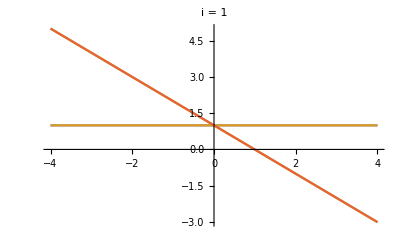
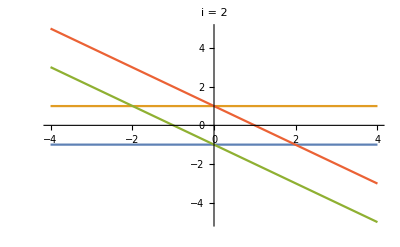
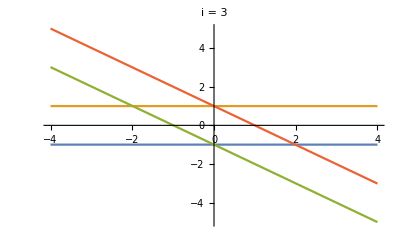
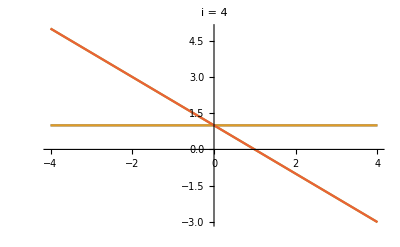
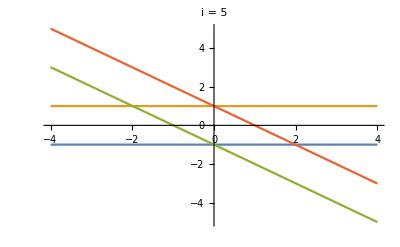
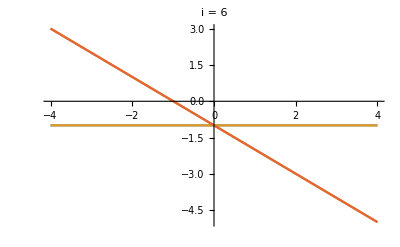
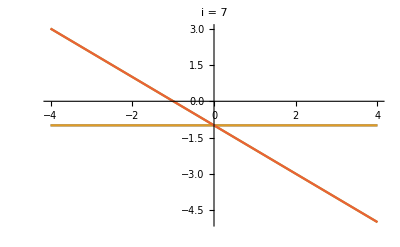
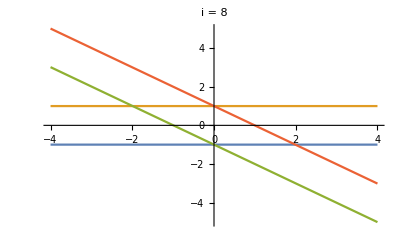

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp1[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
Plot[λ/.e->0.1//Evaluate,{k,-4,4},PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp1]}
]
```

```mathematica
is={6,7,10,11};
```

```mathematica
i=is[[1]];
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp1[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
TableForm[λ]
```

-√(1-e^2)
-√(1-e^2)
-√(1-e^2)-k
-√(1-e^2)-k

```mathematica
Solve[λ[[4]]==0,e]
```

{{e→-√(1-k^2)},{e→√(1-k^2)}}

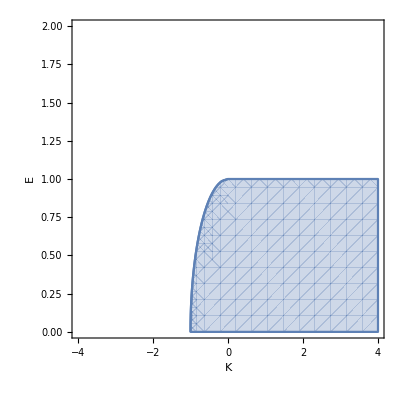

```mathematica
p1=RegionPlot[-√(1-e^2)-k<0,{k,-4,4},{e,0,2}];
p2=ContourPlot[-√(1-e^2)-k==0,{k,-4,4},{e,0,2},FrameLabel->{"K","E"}];
Show[{p2,p1}]
```

#### Order parameter

```mathematica
i=11;
Wp1=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
Wm1=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
TableForm[{Wp1,Wm1}]
```

1-2 e^2+2 ⅈ e √(1-e^2)
1

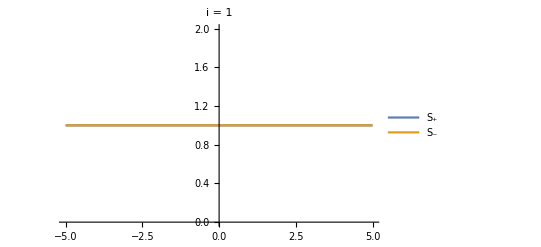
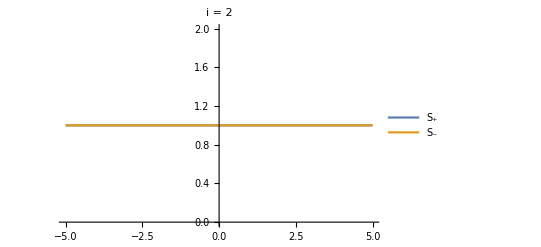
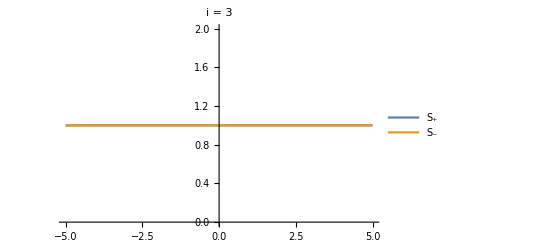
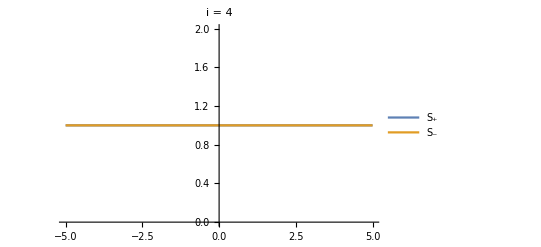
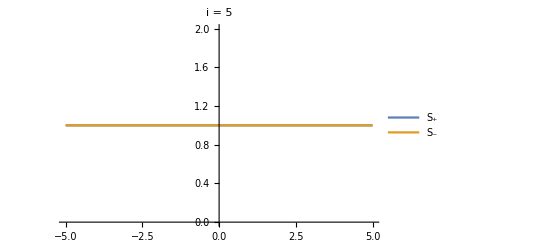
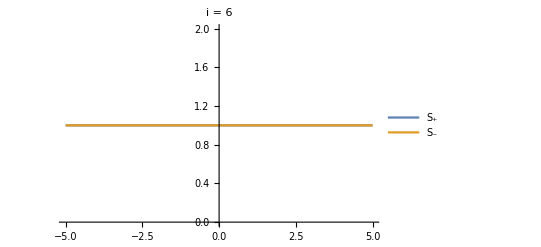
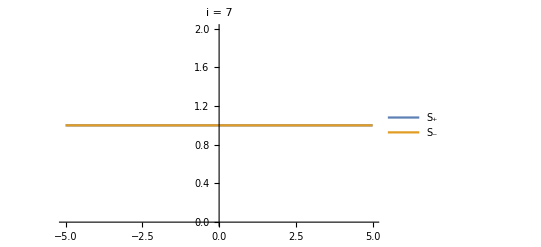
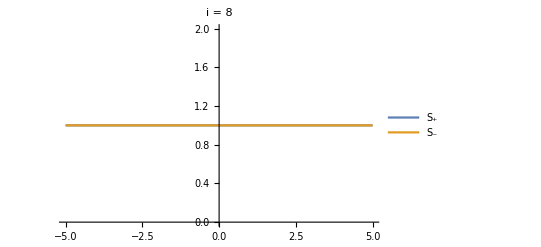

```mathematica
$Assumptions={};
ParallelTable[
Wpsync=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
Wmsync=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
Plot[{Abs[Wpsync]/.e->0.1,Abs[Wmsync]/.e->0.1},{k,-5,5},PlotLabel->"i = "<>ToString[i],PlotLegends->{"S_+","S_-"},LabelStyle->15],
{i,1,Length[fp1]}
]
```

### Fixed point 2

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e3={etemp[[1,1]],etemp[[2,2]]}//FullSimplify;
TableForm[e3]
fp2=Solve[e3==0,{xp,θp}]//FullSimplify
Length[fp2]
```

√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

√(1-e^2 Sec[xp]^2)
e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp→-ArcCos[-e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]}}

32

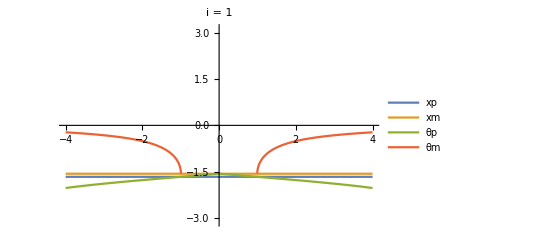
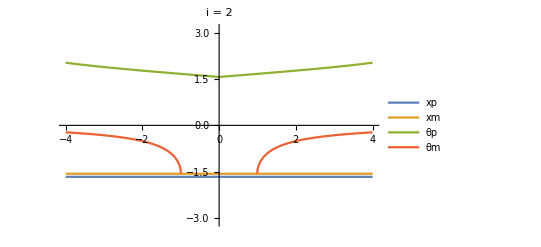
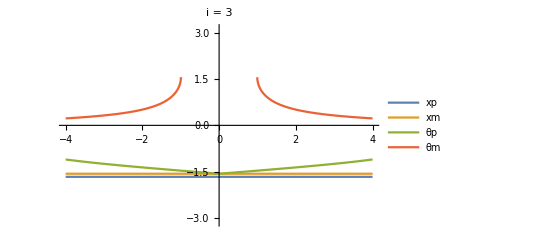
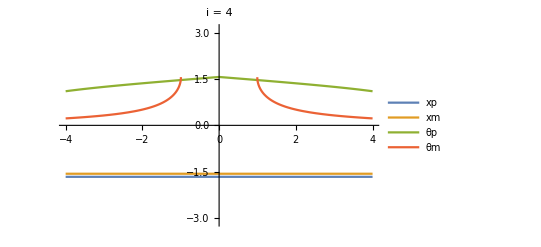
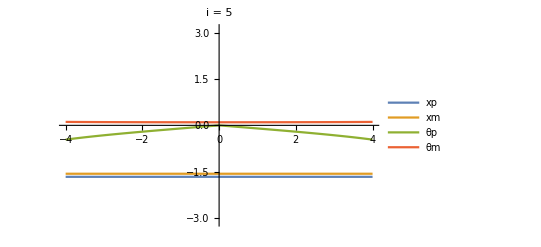
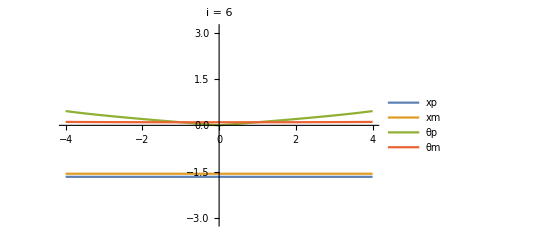
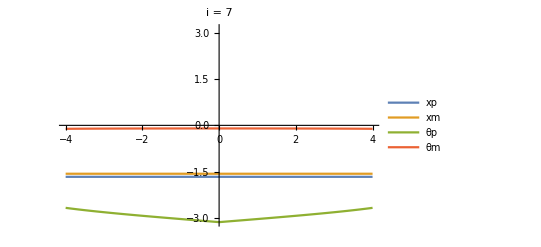
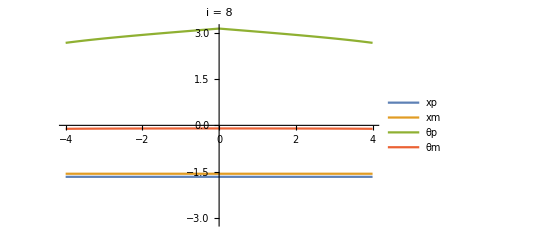

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]/.e->0.1//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15,PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp2]}]
```

#### Eigenvalues

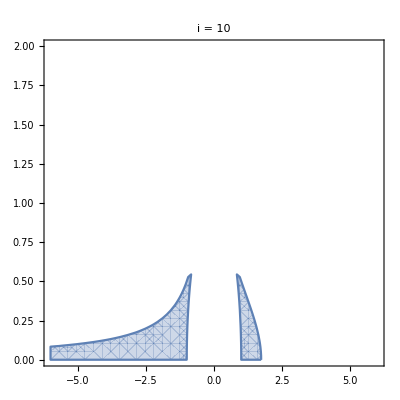
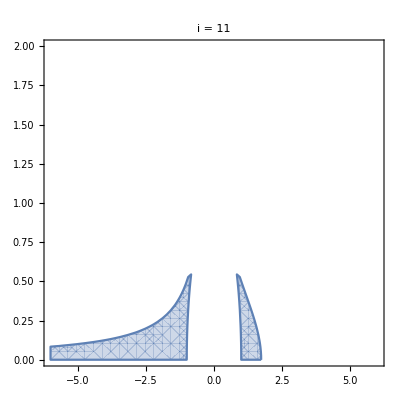
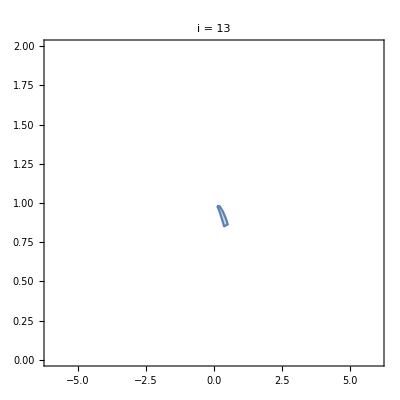
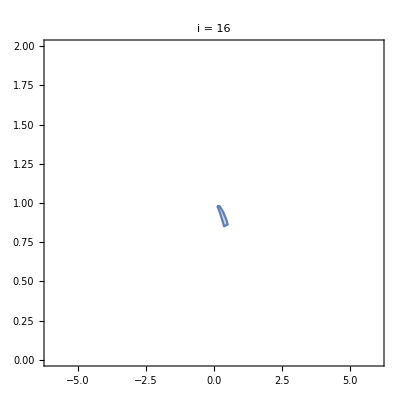
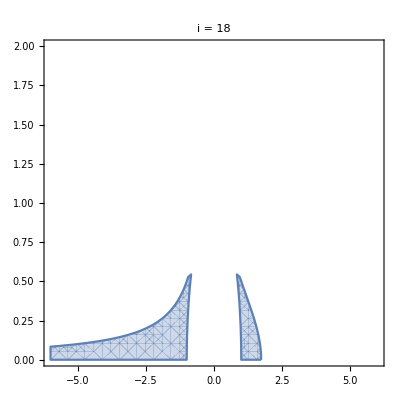
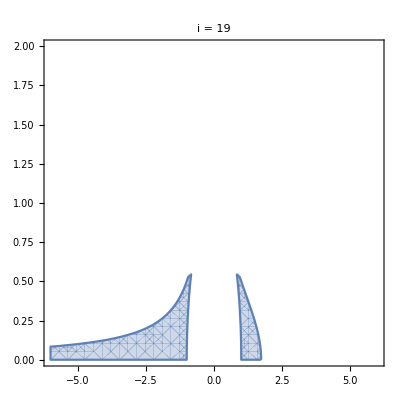
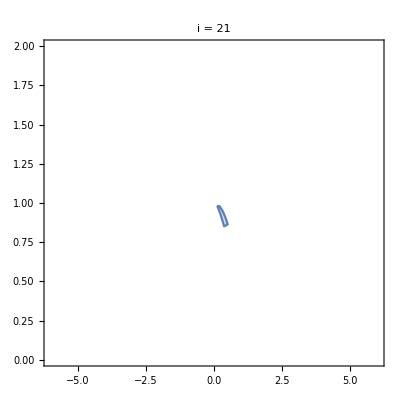
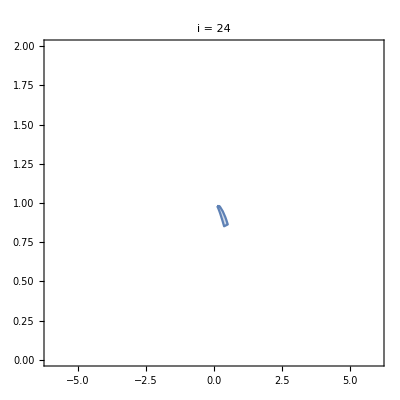
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp2]}
]
```

```mathematica
is={10,11,18,19}
```

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
TableForm[λ]
```

-√(1-e^2)
-(1+(√(1-e^2)-k) k+√(1-4 e^2 k^2))/k
1/2 (k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)+(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k)
1/2 (k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)-(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k)

```mathematica
Solve[-(1+(√(1-e^2)-k) k+√(1-4 e^2 k^2))/k==0,e]//FullSimplify
```

{{e→-√(1-k^2)},{e→√(1-k^2)},{e→-(√(-4+5 k^2-k^4))/(3 k)},{e→(√(-4+5 k^2-k^4))/(3 k)}}

```mathematica
λ[[2]]
```

-(1+(√(1-e^2)-k) k+√(1-4 e^2 k^2))/k

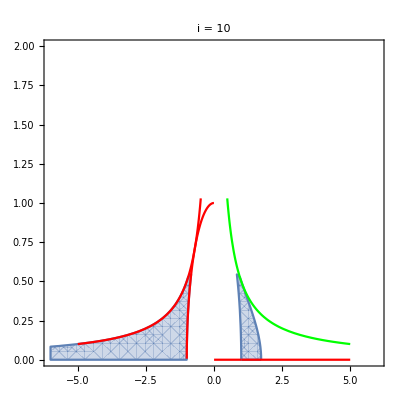

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]];
p2=Plot[{-1/(2k),√(1-k^2)HeavisideTheta[-k],1/(2k)},{k,-5,5},PlotStyle->{Red,Red,Green}];
Show[{p1,p2}]
```

```mathematica
λ/.k->0.9/.e->0.1
```

{-0.994987,-2.29906,-2.4047,-1.10344}

```mathematica
Solve[3 (-1+e^2)+(k+2 e^2 k)^2==0,e]//FullSimplify
```

{{e→-(√(-(3+4 k^2+3 √(1+8 k^2))/k^2))/(2 √2)},{e→(√(-(3+4 k^2+3 √(1+8 k^2))/k^2))/(2 √2)},{e→-(√((-3-4 k^2+3 √(1+8 k^2))/k^2))/(2 √2)},{e→(√((-3-4 k^2+3 √(1+8 k^2))/k^2))/(2 √2)}}

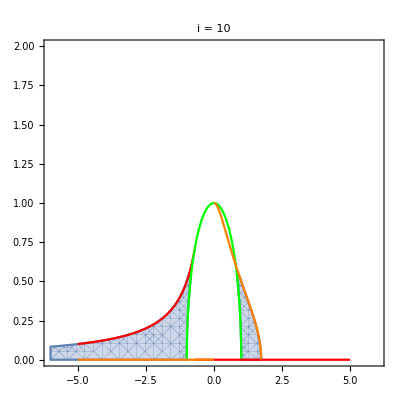

```mathematica
kc=-1/√2;
p2=Plot[{-1/(2k)HeavisideTheta[-(k-kc)],√(1-k^2),(√((-3-4 k^2+3 √(1+8 k^2))/k^2))/(2 √2)HeavisideTheta[k]},{k,-5,5},PlotStyle->{Red,Green,Orange}];
Show[{p1,p2}]
```

```mathematica
FullSimplify[(√((-3-4 k^2+3 √(1+8 k^2))/k^2))/(2 √2),Assumptions->k>0]
```

(√(-3-4 k^2+3 √(1+8 k^2)))/(2 √2 k)

```mathematica
FullSimplify[k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)+(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k]
```

```mathematica
k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)+(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k
```

```mathematica
temp=FullSimplify[Numerator[Together[k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)+(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k]]]
```

-√(1-√(1-4 e^2 k^2))+k^2 √(1-√(1-4 e^2 k^2))-√(1-4 e^2 k^2) √(1-√(1-4 e^2 k^2))-2 e k √(1+√(1-4 e^2 k^2))-√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2))))

```mathematica
removeSqRoot[eqn_,term_]:=Block[{eqn1,Xsol,X},
eqn1=eqn/.term->X;
Xsol=(X/.Solve[eqn1==0,X])[[1]];
Return[Together[Xsol^2-term^2]//Numerator]
]
```

```mathematica
temp1=removeSqRoot[temp,√(1-√(1-4 e^2 k^2))]
```

4 (k^2-2 e^2 k^4-k^2 √(1-4 e^2 k^2)+2 e^2 k^2 √(1-4 e^2 k^2)+e k √(1+√(1-4 e^2 k^2)) √(-k^2 (-4-k^2+16 e^2 k^2+4 √(1-4 e^2 k^2)-8 e^2 √(1-4 e^2 k^2)+k^2 √(1-4 e^2 k^2))))

```mathematica
temp2=removeSqRoot[temp1,√(-k^2 (-4-k^2+16 e^2 k^2+4 √(1-4 e^2 k^2)-8 e^2 √(1-4 e^2 k^2)+k^2 √(1-4 e^2 k^2)))]
```

2 k^2 (1-2 e^2-2 e^4-4 e^2 k^2+8 e^4 k^2+8 e^6 k^2-√(1-4 e^2 k^2)+2 e^2 √(1-4 e^2 k^2)-4 e^4 √(1-4 e^2 k^2)+2 e^2 k^2 √(1-4 e^2 k^2)+4 e^4 k^2 √(1-4 e^2 k^2))

```mathematica
temp3=removeSqRoot[temp2,√(1-4 e^2 k^2)]
```

4 (-3 e^4+6 e^6-3 e^8+4 e^4 k^2+12 e^6 k^2-24 e^8 k^2+8 e^10 k^2-e^4 k^4-20 e^6 k^4-4 e^8 k^4+16 e^12 k^4+4 e^6 k^6+16 e^8 k^6+16 e^10 k^6)

```mathematica
temp4=FullSimplify[temp3]
```

4 e^4 (-1+2 e k) (1+2 e k) (-1+e^2+k^2) (3 (-1+e^2)+(k+2 e^2 k)^2)

```mathematica
(temp4/.k->K)//TeXForm
```

4 e^4 (2 e K-1) (2 e K+1) \left(e^2+K^2-1\right) \left(\left(2 e^2 K+K\right)^2+3 \left(e^2-1\right)\right)

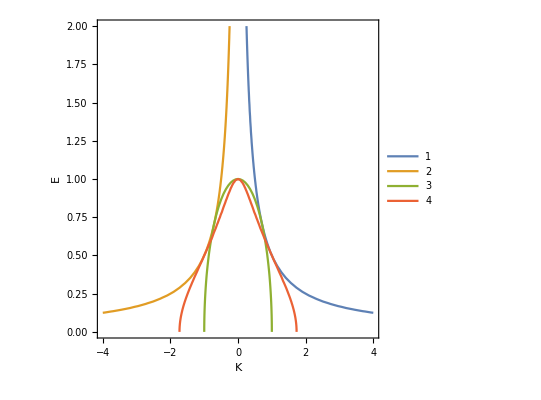

```mathematica
ContourPlot[{-1+2 e k==0,1+2 e k==0,-1+e^2+k^2==0,3 (-1+e^2)+(k+2 e^2 k)^2==0},{k,-4,4},{e,0,2},FrameLabel->{"K","E"},PlotLegends->Table[i,{i,1,4}]]
```

Beautiful

#### Order parameter

```mathematica
θm/.tempSub[[4]]/.fp2[[10]]
```

-ArcSin[(√2 e)/(√(1-√(1-4 e^2 k^2)))]

```mathematica
i=10;
Wp2=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]//TrigExpand//FullSimplify;
Wm2=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]//TrigExpand//FullSimplify;
TableForm[{Wp2,Wm2}]
```

-(e (e-ⅈ √(1-e^2)) (-1+2 ⅈ √(e^2 k^2)+√(1-4 e^2 k^2)))/(-1+√(1-4 e^2 k^2))
(√2 e ⅇ^(-ⅈ (ArcCsc[(√2)/(√(1-√(1-4 e^2 k^2)))]-ArcSin[e])))/(√(1-√(1-4 e^2 k^2)))

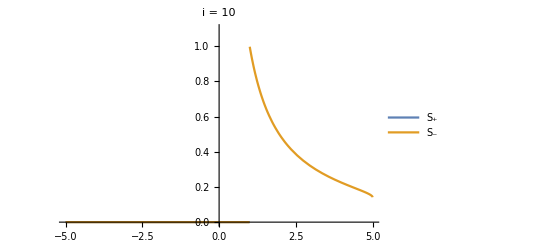
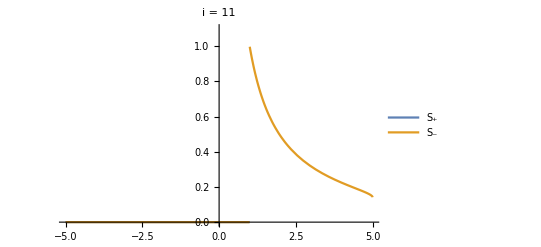
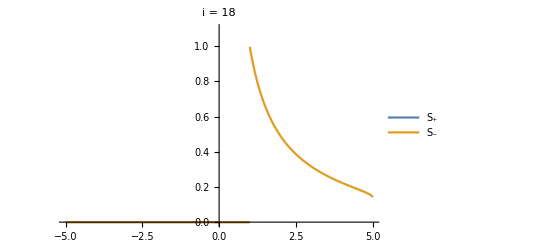
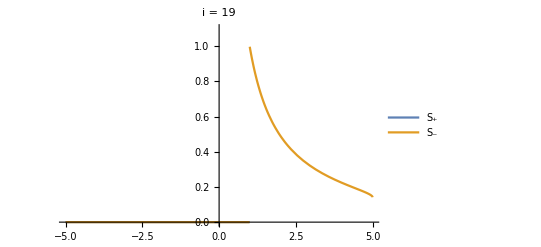

```mathematica
$Assumptions={};
ParallelTable[
Wp2=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]//TrigExpand//FullSimplify;
Wm2=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]//TrigExpand//FullSimplify;
kc=√(1-e^2)/.e->0.1;
Plot[{Abs[Wp2]HeavisideTheta[k-kc],Abs[Wm2]HeavisideTheta[k-kc]/.e->0.1//Evaluate},{k,-5,5},PlotLabel->"i = "<>ToString[i],PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1.1}],
{i,{10,11,18,19}}
]
```

```mathematica
Wm2
```

(√2 e ⅇ^(-ⅈ (ArcCsc[(√2)/(√(1-√(1-4 e^2 k^2)))]-ArcSin[e])))/(√(1-√(1-4 e^2 k^2)))

```mathematica
$Assumptions={0≤e≤1,k∈Reals};
Abs[Wp2]//ComplexExpand//FullSimplify
```

Piecewise[{{(√2 e)/(√(1-√(1-4 e^2 k^2))), 4 e^2 k^2≤1}, {e/(√(e k (2 e k+√(-1+4 e^2 k^2)))), k<0&&4 e^2 k^2>1}, {√((e (2 e k+√(-1+4 e^2 k^2)))/k), True}}]

```mathematica
$Assumptions={0≤e≤1,k∈Reals};
Abs[Wm2]//ComplexExpand//FullSimplify
$Assumptions={};
```

(2 e)/((1+Abs[1-4 e^2 k^2]-2 √Abs[1-4 e^2 k^2] Cos[1/2 Arg[1-4 e^2 k^2]])^(1/4) √(√(1+Abs[1-4 e^2 k^2]-2 √Abs[1-4 e^2 k^2] Cos[1/2 Arg[1-4 e^2 k^2]])+√(1+Abs[1-4 e^2 k^2]+2 √Abs[1-4 e^2 k^2] Cos[1/2 Arg[1-4 e^2 k^2]])-4 e Abs[k] Sin[1/2 (Arg[1-√(1-4 e^2 k^2)]-Arg[1+√(1-4 e^2 k^2)])]))

```mathematica
(√2 e)/(√(1-√(1-4 e^2 k^2)))//TeXForm
```

\frac{\sqrt{2} e}{\sqrt{1-\sqrt{1-4 e^2 k^2}}}

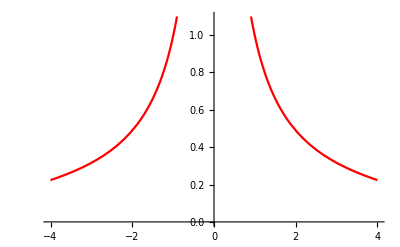

```mathematica
Plot[{Abs[Wm2]}/.e->0.1//Evaluate,{k,-4,4},PlotRange->{0,1.1},PlotStyle->{Blue,Red}]
```

### Fixed point 3 -- Work in progress

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e4={etemp[[1,2]],etemp[[2,1]]}//FullSimplify;
TableForm[e4]
fp4=Solve[e4==0,{xp,θp}]//FullSimplify
Length[fp4]
```

√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp]
√(1-e^2 Sec[θp]^2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[e]}}

32

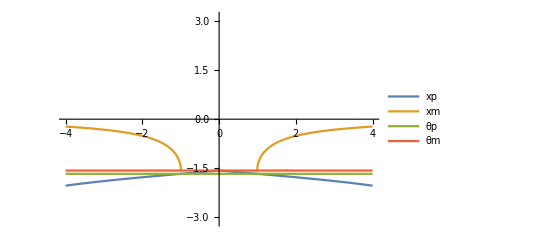
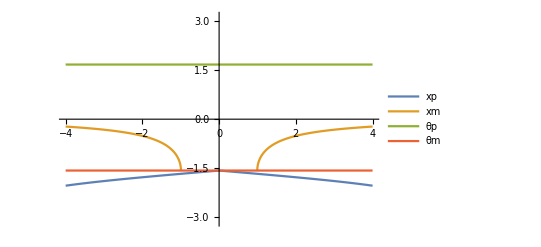
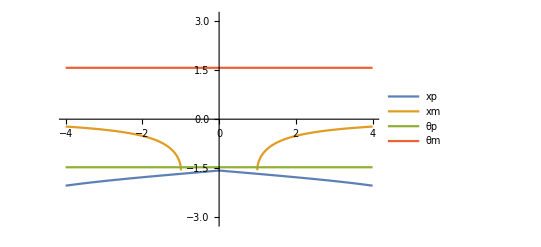
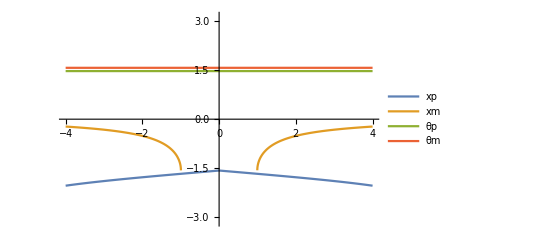
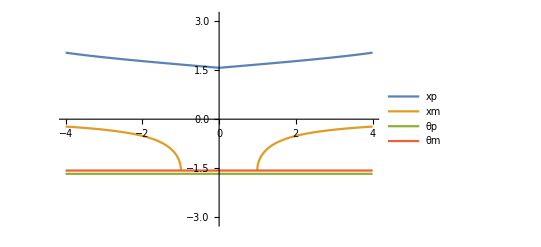
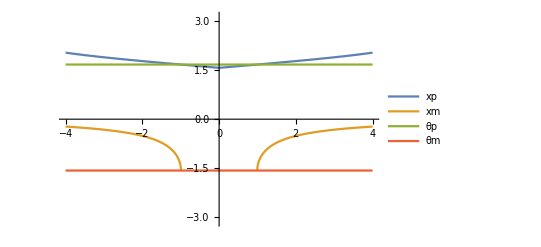
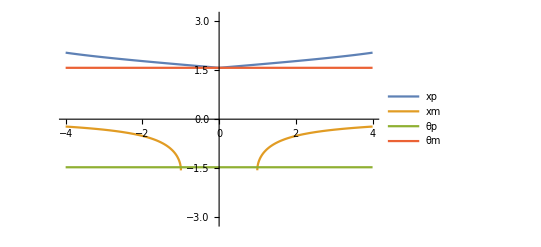
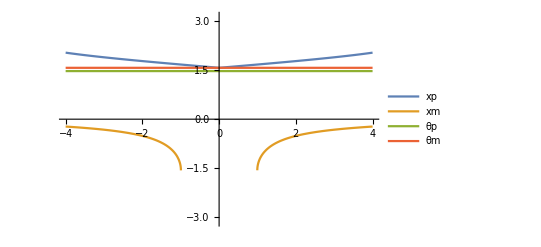

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.tempSub[[4]]/.fp4[[i]]/.e->0.1//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15],
{i,1,Length[fp3]}
]
```

#### Eigenvalues

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp4[[1]]//FullSimplify;
TableForm[J1]
```

(e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2))) | (√(1-√(1-4 e^2 k^2)) √(1+(2 e^2)/(-1+√(1-4 e^2 k^2))))/(√2) | 0 | 0
(√(1-√(1-4 e^2 k^2)) √(1+(2 e^2)/(-1+√(1-4 e^2 k^2))))/(√2) | k+(e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2))/k | 0 | 0
0 | 0 | √(1-e^2) | 0
0 | 0 | 0 | √(1-e^2)+k-(1+√(1-4 e^2 k^2))/k

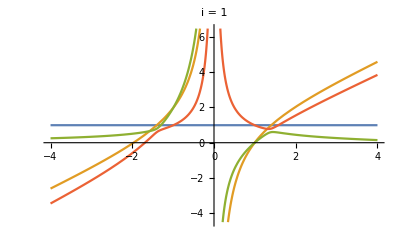
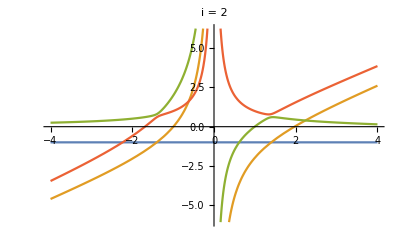
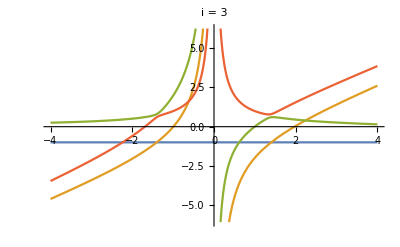
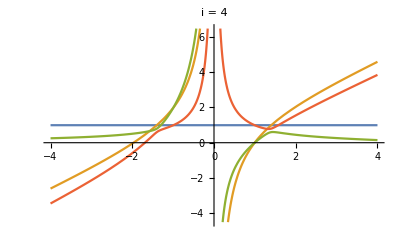
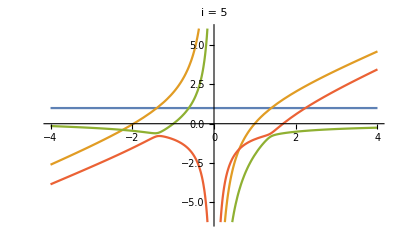
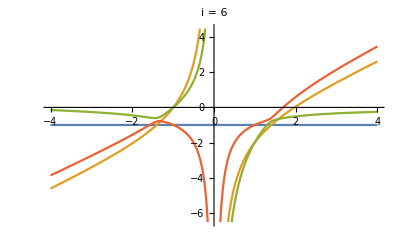
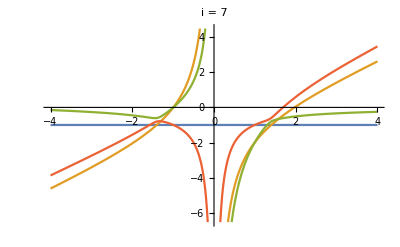
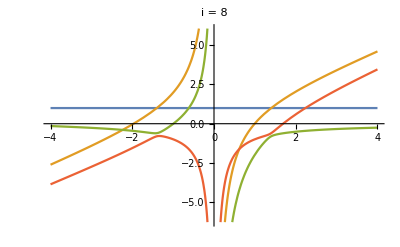
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp4[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
Plot[λ/.e->0.1//Evaluate,{k,-4,4},PlotLabel->"i = "<>ToString[i]],
{i,1,32}
]
```

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp4[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
TableForm[λ]
```

-√(1-e^2)
-(1+(√(1-e^2)-k) k+√(1-4 e^2 k^2))/k
1/2 (k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)+(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k)
1/2 (k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)-(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k)

#### Order parameter

```mathematica
i=1;
Clear[J,K]
Wpsync=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp4[[i]]//TrigExpand//FullSimplify;
Wmsync=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp4[[i]]//TrigExpand//FullSimplify;
TableForm[{Wpsync,Wmsync}]
```

0.466727-0.147412 ⅈ
0.486727-0.0515858 ⅈ

```mathematica
$Assumptions={};
ParallelTable[
Wpsync=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
Wmsync=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
Plot[{Abs[Wpsync]/.e->0.1,Abs[Wmsync]/.e->0.1},{k,-5,5},PlotLabel->"i = "<>ToString[i],PlotLegends->{"S_+","S_-"},LabelStyle->15],
{i,1,Length[fp3]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i=1;
Wpsync=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
Wmsync=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
TableForm[{Wpsync,Wmsync}]
```

0.886076 | 0.688546 | 0.310936 | 0.0102164 | 0.18063 | 0.24521 | 0.243417 | 0.196026 | 0.11562 | 0.0142576 | 0.0923354 | 0.18538 | 0.248819 | 0.27446 | 0.261436 | 0.212888 | 0.134305 | 0.0344033 | 0.0730678 | 0.170056
0.937144 | 0.88544 | 0.785552 | 0.653548 | 0.532634 | 0.434184 | 0.344443 | 0.249712 | 0.143915 | 0.0291687 | 0.0843031 | 0.180826 | 0.246044 | 0.272641 | 0.260179 | 0.211999 | 0.13368 | 0.0339794 | 0.0733386 | 0.170216

```mathematica
$Assumptions={{e,k}∈Reals};
ComplexExpand[Abs[Wpsync]]//FullSimplify
```

Gotta be careful here, I need the fixed points to be real...

## Order parameters J = K

### Defintions

```mathematica
(*Each fixed points*)
Clear[e,k]
{Wp1,Wm1}={1-2 e^2+2 ⅈ e √(1-e^2),1};
{Wp2,Wm2}={(e (e+ⅈ √(1-e^2)) (1+2 ⅈ √(e^2 k^2)-√(1-4 e^2 k^2)))/(-1+√(1-4 e^2 k^2)),1/2 (e+ⅈ √(1-e^2)) √(2+(4 e^2)/(-1+√(1-4 e^2 k^2))) (-ⅈ √(1-√(1-4 e^2 k^2))+√(1+√(1-4 e^2 k^2)))};
{Wp3,Wm3}={(e (e-ⅈ √(1-e^2)) (1+2 ⅈ √(e^2 k^2)-√(1-4 e^2 k^2)))/(-1+√(1-4 e^2 k^2)),1};
```

### Plot

```mathematica
e1=0.1;
kc=1/(√2);
pAnalytic=Plot[{Abs[Wp1]HeavisideTheta[k],Abs[Wm1],Abs[Wp2]}/.e->e1,{k,-4,4},AxesLabel->{Style["K",18,Italic],Style["S_+",18,Italic]},LabelStyle->15,PlotRange->{0,1.1}]
```

-Graphics-

### Numerics

#### Visualization

```mathematica
(*Preamble*)
{dt,n,T}={0.2,2,50}; 
{J,k,b,e}={2,2,1,0.1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.5π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
];

ListPlot[{Wp//Abs,Wm//Abs},AxesLabel->{"time","S"},LabelStyle->15,PlotRange->{0,1.1}]
```

-Graphics-

#### Main plot

```mathematica
data=ParallelTable[
{dt,n,T}={0.1,2,200}; 
{J,k}={k1,k1};
{e,b}={0.1,0.1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k1,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{k1,Sp,Sm},
{k1,-2,2,0.025}
];
Clear[e,k,b]
pNumerical=ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"K"},PlotLegends->{"S+","S-"},AxesStyle->15,PlotStyle->All,PlotLabel->Style["E = "<>ToString[e1],18]];
Show[{pAnalytic,pNumerical}]
```

-Graphics-

## Bifurcation diagram (E,K) for J = K

### Version 1

```mathematica
curve1=√(1-e^2)-k;
curve2=1+2 e k;
curve3=e-(√(-3-4 k^2+3 √(1+8 k^2)))/(2 √2 k);
kc2=√(1/2 (3-√3));
p1=Plot[{1HeavisideTheta[k],
(*Bistable*)
√(1-k^2)HeavisideTheta[-k],-1/(2 k)HeavisideTheta[-k-1/(√2)]
},{k,-4,2},AxesLabel->{Style["K",Italic,16],Style["E",Italic,16]},PlotStyle->{Black,Black},PlotRange->{{-4,2},{0,1.2}},
Epilog->{
Text[Style["FP 1",15],{1,0.70}],
Text[Style["FP 2 + FP 3",15],{-2,0.125}],
Text[Style["Periodic",15],{-2.5,0.8}]
}
]

SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-J-K.png",p1];
```

-Graphics-

Point of interstion:  (K^*,(E^*)^)=(-1/(√2),1/(√2)). Here all three fixed points are the same? Should be able to see this in the S plots.

```mathematica
Solve[(√(-3-4 k^2+3 √(1+8 k^2)))/(2 √2 k)==√(1-k^2),k]//N
```

{{k→0.796225}}

### Version 2

```mathematica
curve1=√(1-e^2)-k;
curve2=1+2 e k;
curve3=e-(√(-3-4 k^2+3 √(1+8 k^2)))/(2 √2 k);
kc1=1/(√2);
kc2=√(1/2 (3-√3));
p1=Plot[{1HeavisideTheta[k],
(*Bistable*)
√(1-k^2)HeavisideTheta[-k],-1/(2 k)HeavisideTheta[-k-kc1],
(*Tristable region*)
√(1-k^2)HeavisideTheta[k-kc2],(√(-3-4 k^2+3 √(1+8 k^2)))/(2 √2 k)HeavisideTheta[k-kc2]
},{k,-2.5,2},AxesLabel->{Style["K",Italic,16],Style["E",Italic,16]},PlotStyle->{Black,Black,Black,Black},PlotRange->{{-2.5,2},{0,1.2}},
Epilog->{
Text[Style["1",20],{1,0.8}],
Text[Style["2,3",20],{-2,0.125}],
Text[Style["periodic",17],{-1.5,0.8}],
Text[Style["1,2,3",18],{1.3,0.15}],
Text[Style["SNIPER",Blue,14],{-1.5,0.45}],
Text[Style["SNIPER",Blue,14],{1,1.1}],
Text[Style["SN",Blue,14],{-0.75,0.2}],
Text[Style["SN",Blue,14],{0.75,0.2}],
Text[Style["SN",Blue,14],{1.5,0.4}],
PointSize[Large],Point[{-1/(√2),1/(√2)}],Point[{√(1/2 (3-√3)),√(1/2 (-1+√3))}]
}
]

SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-J-K.png",p1];
```

-Graphics-

Point of interstion:  (K^*,(E^*)^)=(-1/(√2),1/(√2)). Here all three fixed points are the same? Should be able to see this in the S plots.

```mathematica
Solve[(√(-3-4 k^2+3 √(1+8 k^2)))/(2 √2 k)==√(1-k^2),k]
```

{{k→√(1/2 (3-√3))}}

```mathematica
(√(-3-4 k^2+3 √(1+8 k^2)))/(2 √2 k)/.k->√(1/2 (3-√3))//FullSimplify
```

√(1/2 (-1+√3))

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}, {Ex,_Real}, {Eθ, _Real}, {pin, _Real, 2}, {b1,_Real},{b2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
vel[[1,i]] = Ex + b1*Sin[pin[[1,i]] - z[[1,i]]];
vel[[2,i]] = Eθ + b2*Sin[pin[[2,i]] - z[[2,i]]];
];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji]*Cos[thetaji]/N[n];
thetatemp=k*Sin[thetaji]*Cos[xji]/N[n];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel
(*vel/N[n]*)
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
k2=F[z+dt/2 k1,n,J,k,Ex,Eθ,pin,b1,b2];
k3=F[z+dt/2 k2,n,J,k,Ex,Eθ,pin,b1,b2];
k4=F[z+dt k3,n,J,k,Ex,Eθ,pin,b1,b2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin,x1,θ1,x2,θ2,ξ1,ξ2,η1,η2,index,n},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
n=Length[x];
index=Round[n/2];
{x1,θ1}={x[[1]],θ[[1]]};
{x2,θ2}={x[[index]],θ[[index]]};
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},Epilog->{Cyan,PointSize[0.025],Point[{x1,θ1}//mod],Magenta,Point[{x2,θ2}//mod]}];

(*Scatter plot in (ξ,θ) space*)
{ξ1,η1}={x[[1]]+θ[[1]],x[[1]]-θ[[1]]};
{ξ2,η2}={x[[index]]+θ[[index]],x[[index]]-θ[[index]]};
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]},Epilog->{Cyan,PointSize[0.025],Point[{ξ1,η1}//mod],Magenta,Point[{ξ2,η2}//mod]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];
```

Compile::nogen: A library could not be generated from the compiled function.